## Load and format data

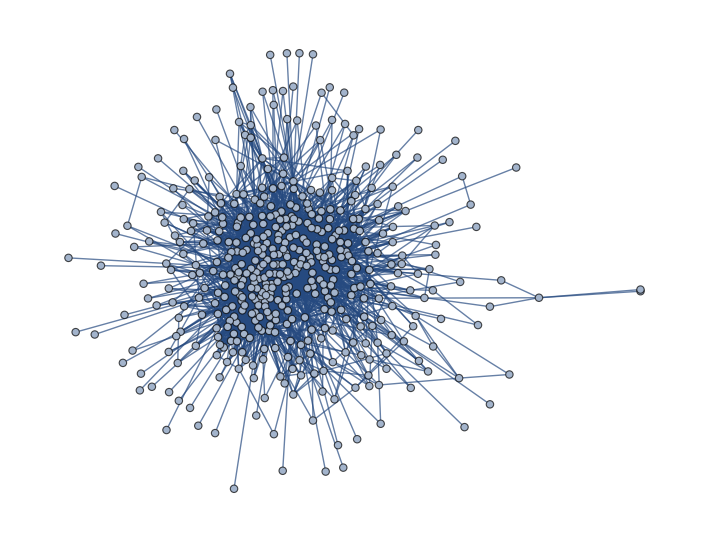

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
data = Import["/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/Full_Kinome_Network_Compiled.txt","Table"];
newdat = Drop[data,3];
net = Map[#[[1]]<->#[[2]] &,newdat];
g = Graph[net]
labels = {"AAPK1", "AAPK2", "ABL1", "ABL2", "ACK1", "ACV1B" ,"ACV1C" ,"ACVL1" ,"ACVR1", "ADCK3" ,"ADCK4" ,"AGK" ,"AKT1" ,"AKT2" ,"AKT3" ,"ALK" ,"AMHR2", "ANPRA" ,"ARAF" ,"ARBK1" ,"ARBK2" ,"ATM" ,"ATR" ,"AURKB" ,"AURKC", "AVR2A" ,"AVR2B" ,"BLK", "BMP2K", "BMPR2", "BMR1A", "BMR1B", "BMX", "BRAF", "BRD2", "BRD3" ,"BRD4", "BRSK1" ,"BRSK2", "BTK", "BUB1", "BUB1B" ,"CD11A" ,"CD11B" ,"CDC7" ,"CDK1" ,"CDK12" ,"CDK13", "CDK14", "CDK15", "CDK16", "CDK17" ,"CDK18" ,"CDK19" ,"CDK2", "CDK20", "CDK3", "CDK4" ,"CDK5" ,"CDK6" ,"CDK7" ,"CDK8", "CDK9" ,"CDKL1" ,"CDKL3", "CDKL5", "CHK1", "CHK2", "CLK1", "CLK2" ,"CLK3" ,"CLK4" ,"CSF1R", "CSK" ,"CSK21" ,"CSK22", "CSKP" ,"DAPK1" ,"DAPK2" ,"DAPK3" ,"DCLK2", "DCLK3" ,"DDR1", "DDR2" ,"DMPK" ,"DUSTY" ,"DYR1A" ,"DYR1B" ,"DYRK2" ,"DYRK3" ,"DYRK4" ,"E2AK1" ,"E2AK2", "E2AK3" ,"E2AK4", "EF2K" ,"EGFR", "EPHA1" ,"EPHA2" ,"EPHA3" ,"EPHA4" ,"EPHA5", "EPHA6" ,"EPHA7" ,"EPHA8" ,"EPHAA" ,"EPHB1" ,"EPHB2", "EPHB3", "EPHB4" ,"EPHB6" ,"ERBB2" ,"ERBB3", "ERBB4" ,"ERN1" ,"FAK1" ,"FAK2" ,"FAKD5" ,"FER", "FES", "FGFR1" ,"FGFR2" ,"FGFR3", "FGFR4", "FGR", "FLT3" ,"FRK", "FYN", "GAK" ,"GRK5", "GRK6" ,"GRK7" ,"GSK3A" ,"GSK3B" ,"GUC2C" ,"GUC2D", "GWL" ,"HASP" ,"HCK", "HIPK1" ,"HIPK2" ,"HIPK3", "HIPK4" ,"HUNK", "HXK1", "HXK2" ,"ICK", "IGF1R" ,"IKKA" ,"IKKB" ,"IKKE", "ILK", "INSR" ,"INSRR" ,"IRAK1", "IRAK2" ,"IRAK3" ,"IRAK4", "ITK" ,"JAK1" ,"JAK2" ,"JAK3" ,"K6PF" ,"K6PL" ,"K6PP" ,"KAD1", "KAD2", "KALRN", "KAPCA" ,"KAPCB" ,"KAPCG" ,"KC1A" ,"KC1D" ,"KC1E" ,"KC1G1" ,"KC1G2" ,"KC1G3", "KCC1A", "KCC1D", "KCC1G" ,"KCC2A" ,"KCC2B", "KCC2D" ,"KCC2G" ,"KCC4" ,"KCRM", "KGP1" ,"KGP2" ,"KHK" ,"KIT" ,"KKCC1" ,"KKCC2" ,"KPCA" ,"KPCB", "KPCD" ,"KPCD1" ,"KPCD2", "KPCD3" ,"KPCE", "KPCG" ,"KPCI", "KPCL" ,"KPCT", "KPCZ" ,"KPYM" ,"KS6A1" ,"KS6A2" ,"KS6A3" ,"KS6A4" ,"KS6A5", "KS6A6" ,"KS6B1" ,"KS6B2" ,"KSR1" ,"KSR2" ,"KSYK" ,"KT3K" ,"LATS1" ,"LATS2", "LCK" ,"LIMK1" ,"LIMK2" ,"LMTK1" ,"LMTK2", "LRRK1", "LRRK2" ,"LTK" ,"LYN" ,"M3K1" ,"M3K10" ,"M3K11" ,"M3K12", "M3K13", "M3K14", "M3K2" ,"M3K3" ,"M3K4" ,"M3K5", "M3K6" ,"M3K7", "M3K8" ,"M3KL4", "M4K1" ,"M4K2" ,"M4K3" ,"M4K4" ,"M4K5", "MAK", "MAPK2" ,"MAPK3" ,"MAPK5" ,"MARK1" ,"MARK2" ,"MARK3" ,"MARK4" ,"MAST1", "MAST2", "MAST3", "MATK", "MELK" ,"MERTK", "MET", "MINK1" ,"MK01" ,"MK03" ,"MK04" ,"MK06" ,"MK07" ,"MK08" ,"MK09" ,"MK10" ,"MK11" ,"MK12" ,"MK13" ,"MK14" ,"MK15" ,"MKNK1", "MKNK2" ,"MLKL" ,"MLTK", "MOK", "MOS" ,"MP2K1" ,"MP2K2" ,"MP2K3" ,"MP2K4" ,"MP2K5" ,"MP2K6" ,"MP2K7" ,"MRCKA" ,"MRCKB" ,"MRCKG", "MST4", "MTOR" ,"MYLK", "MYLK2" ,"MYLK3", "MYO3A" ,"NDK3", "NDK7", "NDKA", "NDKB" ,"NDKM" ,"NEK1" ,"NEK10" ,"NEK11" ,"NEK2", "NEK3" ,"NEK6" ,"NEK7" ,"NEK8" ,"NEK9" ,"NLK" ,"NRBP" ,"NTRK1", "NTRK2", "NTRK3", "NUAK1" ,"NUAK2" ,"OBSCN" ,"OXSR1", "P3C2A" ,"P4K2B" ,"PAK1" ,"PAK2" ,"PAK3", "PAK4", "PAK6", "PAK7" ,"PASK", "PCKGM", "PDK1", "PDK2" ,"PDK3", "PDPK1", "PDXK" ,"PGFRA", "PGFRB", "PGK1" ,"PHKG1", "PHKG2", "PI3R4", "PI42A" ,"PI42B", "PI42C", "PI4KA", "PI51A", "PI51B" ,"PI51C", "PIM1" ,"PIM2", "PINK1", "PK3C3", "PK3CA" ,"PK3CB", "PK3CD" ,"PK3CG" ,"PKN1", "PKN2", "PKN3", "PLK1" ,"PLK2" ,"PLK3", "PLK4" ,"PMYT1" ,"PRKDC", "PRKX", "PRKY" ,"PRP4B", "PRPK", "PTK6", "PTK7" ,"RAF1", "RET" ,"RIOK1" ,"RIOK2" ,"RIOK3" ,"RIPK1" ,"RIPK2" ,"RIPK3" ,"RIPK4" ,"ROCK1" ,"ROCK2", "RON" ,"ROR1", "ROR2", "ROS1" ,"RYK" ,"SG196" ,"SGK1", "SGK2", "SGK3" ,"SIK1" ,"SIK2" ,"SIK3", "SLK" ,"SMG1" ,"SNRK", "SRC" ,"SRMS", "SRPK1", "SRPK2", "SRPK3", "ST17B", "ST38L", "STK10", "STK11" ,"STK16" ,"STK24" ,"STK25" ,"STK3", "STK33", "STK35", "STK36", "STK38" ,"STK39" ,"STK4" ,"STK40" ,"STK6" ,"STRAA" ,"STRAB", "STYK1" ,"TAOK1", "TAOK2", "TAOK3", "TBK1", "TEC" ,"TESK1", "TEX14", "TGFR1" ,"TGFR2", "TIE1", "TIE2" ,"TIF1A" ,"TIF1B" ,"TITIN" ,"TLK1", "TLK2", "TNIK" ,"TNK1", "TOPK", "TRIB1", "TRIB2", "TRIB3" ,"TRIO", "TRPM6", "TRPM7" ,"TSSK1", "TSSK2" ,"TSSK4" ,"TTBK1" ,"TTBK2" ,"TTK" ,"TXK", "TYK2" ,"TYRO3" ,"UFO" ,"UHMK1", "ULK1", "ULK2", "VGFR1" ,"VGFR2", "VGFR3", "VRK1", "VRK2", "VRK3" ,"WEE1" ,"WNK1" ,"WNK2", "WNK3" ,"WNK4" ,"YES", "ZAP70"};
```

```mathematica
labTable = Table[labels[[i]] -> labels[[i]],{i,Length[labels]}];
```

```mathematica
<<IGraphM`;
```

Evaluate IGDocumentation[] to get started.

## Cluster network using different algorithms

```mathematica
Ggreedy = IGCommunitiesGreedy[g];
Gspinglass = IGCommunitiesSpinGlass[g];
Gwalktrap = IGCommunitiesWalktrap[g];
```

```mathematica
Ggreedy["Communities"][[1]]
```

{PAK1,ATR,PRKDC,PHKG1,PHKG2,NEK2,GSK3B,MARK4,DAPK3,MARK2,WEE1,CSK21,ATM,MOS,KAPCA,MK15,TGFR1,AMHR2,BRSK1,STK11,TOPK,ARBK1,EF2K,AAPK2,PLK4,TAOK2,LATS1,TIF1A,TIF1B,PLK1,CHK2,MARK1,STRAB,KS6B1,STRAA,TAOK1,ILK,BUB1B,ERN1,MK07,SGK1,PDK2,OXSR1,PI3R4,PK3C3,AAPK1,PLK3,NEK6,KKCC1,CHK1,TLK1,TAOK3,TSSK1,NEK9,CDK7,KKCC2,KCC1A,KS6B2,NEK7,TRPM7,TRPM6,KCC4,DAPK2,CSK22,CDK9,TLK2,BRSK2,AKT1,KCC1D,CDK2,NUAK2,AURKB,CDK4,STK35,CDK6,CDKL1,KC1A,E2AK4,MYO3A,TSSK4,STK3,STK4,LATS2,CDC7,CLK2,CLK3,SG196,SNRK,CDK5,KC1D,GAK,ST38L,STK24,BUB1,WNK4,CSK,NEK11,AKT2,MST4,STK25,TTBK1,TTBK2,LMTK2,CDK1,KHK,MELK,VRK1,VRK3,KPCD2,KC1E,CSKP,SIK3,ULK2,ULK1,MAST1,MAST3,DYR1A,SRPK1,SRPK2,NUAK1,LRRK2,NDK7,PLK2,KAPCB,SIK2,SIK1,MTOR,STK38,TTK,NRBP,PIM2,DDR1,CDK13,CDK16,KAPCG,CDK17,CD11A,CDK20,MAK,CD11B,CDK15,CDK19,CDK8,CDK3,RIOK2,RIOK1,PINK1,ICK,HXK1,GRK5,HASP,CLK4,CDK14,CDK18,STYK1,CDK12,DCLK3,CDKL3,CLK1,AURKC,ARBK2,ADCK4,PRPK,KCC1G,NEK1,STK33,TRIB2,PCKGM,KC1G2,E2AK1,KC1G1,NEK3,MINK1,KC1G3,STK6,ST17B,TNK1,GRK7,TEX14}

## Write output files

```mathematica
Length[Ggreedy["Communities"]]
```

8

```mathematica
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/greedycluster1.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Ggreedy["Communities"][[1]]];
Close[file];
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/greedycluster2.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Ggreedy["Communities"][[2]]];
Close[file];
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/greedycluster3.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Ggreedy["Communities"][[3]]];
Close[file];
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/greedycluster4.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Ggreedy["Communities"][[4]]];
Close[file];
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/greedycluster5.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Ggreedy["Communities"][[5]]];
Close[file];
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/greedycluster6.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Ggreedy["Communities"][[6]]];
Close[file];
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/greedycluster7.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Ggreedy["Communities"][[7]]];
Close[file];
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/greedycluster8.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Ggreedy["Communities"][[8]]];
Close[file];
```

```mathematica
Length[Gspinglass["Communities"]]
```

7

```mathematica
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/spinglasscluster1.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Gspinglass["Communities"][[1]]];
Close[file];
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/spinglasscluster2.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Gspinglass["Communities"][[2]]];
Close[file];
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/spinglasscluster3.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Gspinglass["Communities"][[3]]];
Close[file];
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/spinglasscluster4.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Gspinglass["Communities"][[4]]];
Close[file];
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/spinglasscluster5.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Gspinglass["Communities"][[5]]];
Close[file];
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/spinglasscluster6.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Gspinglass["Communities"][[6]]];
Close[file];
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/spinglasscluster7.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Gspinglass["Communities"][[7]]];
Close[file];
fileName = "/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/spinglasscluster8.txt";
file = OpenWrite[fileName,PageWidth-> Infinity];
Export[file,Gspinglass["Communities"][[8]]];
Close[file];
```

Part::partw: Part 8 of {{PAK1,ATR,PRKDC,PHKG1,PHKG2,NEK2,MARK4,DAPK3,MARK2,WEE1,CSK21,ATM,KAPCA,BRSK1,STK11,AAPK2,PLK4,PAK4,LATS1,TIF1A,TIF1B,PLK1,CHK2,MARK1,STRAA,TAOK1,BUB1B,ERN1,PI3R4,PK3C3,AAPK1,PLK3,NEK6,KKCC1,CHK1,TLK1,TAOK3,NEK9,CDK7,KKCC2,KCC1A,NEK7,KCC4,CSK22,MAST2,STK36,CDK9,BRSK2,KCC1D,CDK2,«91»},«5»,{NDKA,NDKM,NDK3,«5»,KAD2,PDXK,SLK}} does not exist.

## Visualize networks with subnetworks

```mathematica
g1greedy = CommunityGraphPlot[g,Ggreedy["Communities"],Method->"Hierarchical",CommunityLabels->{Style["SN1",Black,18],Style["SN2",Black,18],Style["SN3",Black,18],Style["SN4",Black,18],Style["SN5",Black,18],Style["SN6",Black,18],Style["SN7",Black,18],Style["SN8",Black,18]}]
```

```mathematica
g1greedylabels = CommunityGraphPlot[g,Ggreedy["Communities"],Method->"Hierarchical",VertexLabels->labTable,CommunityLabels->{Style["SN1",Black,18],Style["SN2",Black,18],Style["SN3",Black,18],Style["SN4",Black,18],Style["SN5",Black,18],Style["SN6",Black,18],Style["SN7",Black,18],Style["SN8",Black,18]}]
```

-Graphics-

```mathematica
Subgraph[g,Ggreedy["Communities"][[1]],VertexLabels->labTable,GraphLayout->"RadialDrawing"];
```

```mathematica
Subgraph[g,Ggreedy["Communities"][[2]],VertexLabels->labTable,GraphLayout->Automatic];
```

```mathematica
Subgraph[g,Ggreedy["Communities"][[2]]];
```

```mathematica
Subgraph[g,Ggreedy["Communities"][[2]],VertexLabels->labTable,GraphLayout->"SpringEmbedding",PlotLabel->Style["Subnetwork 2 (SN2)",Black,Bold,14]];
```

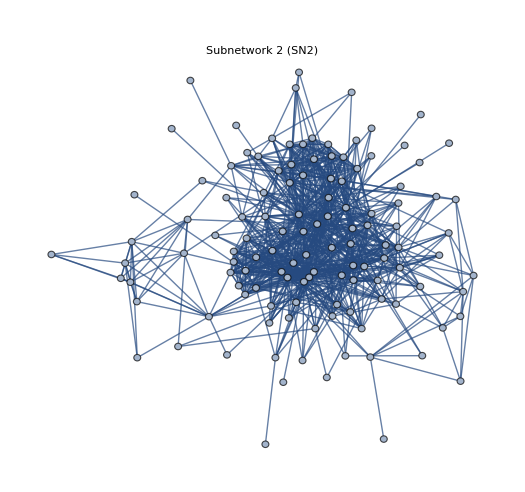

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Subgraph[g,Ggreedy["Communities"][[2]],GraphLayout->"SpringEmbedding",PlotLabel->Style["Subnetwork 2 (SN2)",Black,Bold,14]]
```

```mathematica
g1spinglass = CommunityGraphPlot[g,Gspinglass["Communities"],Method->"Hierarchical"]
```

-Graphics-

```mathematica
g1walktrap = CommunityGraphPlot[g,Gwalktrap["Communities"],Method->"Hierarchical"]
```

-Graphics-

```mathematica
Gspectral = FindGraphCommunities[g,Method->"Spectral"];
```

```mathematica
g1spectral=CommunityGraphPlot[g,Gspectral,Method->"Hierarchical"]
```

-Graphics-

```mathematica
dataconsensus = Import["/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/consensusspinglassclusters_formathematica.txt","Table"]
```

{{PAK1,CSK22,CD11A,CD11B},{ERBB2,RON,TYRO3,KIT,SRC,MATK,TEC,FGR,KSYK,FAK1,VGFR2,VGFR1,TYK2,BTK,FAK2,PK3CG,M4K1,PGFRB,PK3CA,PGFRA,ZAP70,PK3CB,AKT3,MET,ITK,BMX,NTRK1,M4K5,DDR2,TXK,GUC2C,MK15,ERBB4,ERBB3,PTK6,LCK,UFO,JAK3,TIE1,TIE2,EPHB1,KCC2G,PDK1,KCC2A,EGFR,VGFR3,FGFR3,JAK2,FES,FGFR1,FGFR2,FYN,HCK,JAK1,PI42A,KCC2B,KCC2D,FGFR4,CSK,PIM1,FER,ACK1,CSF1R,NTRK2,ABL2,AKT2,TRIB3,PK3CD,GUC2D,ROR1,BRAF,BLK,PDK3,FRK,EPHA5,KT3K,FLT3,SRMS},{YES,LYN,EPHA8,EPHA2,ABL1,MK06,OBSCN,EPHB2,PAK2,RYK,EPHB3,EPHB6,TRIO,LIMK1,ROCK1,LIMK2,MRCKA,KALRN,EPHA4,AGK,EPHA3,MK04,HIPK3,PAK3,ROCK2,UHMK1,CDKL5,EPHB4,EPHA1,PTK7,DDR1,MOK,EPHA7,BMP2K,CLK4,EPHA6,EPHAA,HUNK},{KPCA,KPCD,KPCT,MK03,MK01,MP2K1,ARAF,KS6A2,KS6A4,KSR2,KPCE,NTRK3,KS6A3,MP2K2,KS6A1,KPCZ,GSK3A,KPCB,GSK3B,PDPK1,RIPK4,HXK2,KPCD1,KPCG,KPYM,RET,TITIN,TOPK,ARBK1,STK39,MARK3,DAPK1,PMYT1,KS6A5,KS6B1,MK07,SGK1,PDK2,SGK3,SGK2,KS6B2,KPCL,KPCD3,AKT1,IGF1R,RAF1,INSR,WNK1,WNK4,KSR1,INSRR,DMPK,LTK,WNK2,HIPK1,KGP1,MTOR,NRBP,KS6A6,PIM2,DYRK2,ROS1,ROR2,GWL,HIPK4,DYRK4,STYK1,ARBK2,PRPK,DYRK3,TSSK2,PAK7,DCLK2,PRKX,GRK6,WNK3},{ATR,PRKDC,PHKG2,NEK2,MARK4,DAPK3,WEE1,CSK21,ATM,KAPCA,BRSK1,STK11,AAPK2,PLK4,LATS1,TIF1A,TIF1B,PLK1,CHK2,MARK1,STRAA,TAOK1,BUB1B,ERN1,PI3R4,PK3C3,AAPK1,PLK3,NEK6,KKCC1,CHK1,TLK1,TAOK3,NEK9,CDK7,KKCC2,KCC1A,NEK7,KCC4,MAST2,STK36,CDK9,BRSK2,KCC1D,CDK2,AURKB,CDK4,CDK6,KC1A,E2AK4,STK3,STK4,LATS2,CDC7,CLK2,CLK3,SNRK,CDK5,KC1D,GAK,ST38L,STK24,BUB1,NEK11,MST4,STK25,TTBK1,TTBK2,LMTK2,CDK1,MELK,VRK1,VRK3,KC1E,CSKP,SIK3,ULK2,ULK1,MAST1,MAST3,SRPK1,SRPK2,NUAK1,LRRK2,PLK2,KAPCB,SIK2,SIK1,STK38,TTK,CDK13,CDK16,KAPCG,CDK17,CDK20,MAK,CDK15,CDK19,CDK8,CDK3,RIOK2,RIOK1,ICK,HXK1,GRK5,HASP,PRP4B,CDK14,CDK18,CDK12,DCLK3,CDKL3,CLK1,SRPK3,AURKC,KCC1G,TRIB2,PCKGM,NEK3,KC1G3,STK6,TNK1,TEX14},{K6PF,K6PL,ILK,KHK,TESK1,K6PP,ADCK4},{PHKG1},{E2AK2,M3K5,IKKB,M3K4,TRIB1,MK14,DYR1B,MAPK5,MKNK1,IRAK1,MK08,PKN1,MP2K6,MK12,MLTK,IKKA,M3K8,MP2K4,M3K14,IRAK2,IRAK3,IRAK4,M3K12,M3K11,MP2K7,M4K2,M3K10,MAPK3,MP2K3,EF2K,M3K7,M3K2,MK13,TAOK2,MK09,MK10,M3K3,STRAB,M3K6,RIPK1,PKN2,M4K4,MK11,E2AK3,M3K13,RIPK3,NLK,HIPK2,TRPM7,TRPM6,MAPK2,RIPK2,TBK1,ALK,M3K1,MLKL,TNIK,M3KL4,DYR1A,NDK7,RIOK3,ADCK3,MRCKG,M4K3,PINK1,STK40,NEK10,MYLK3,MINK1,PRKY,STK10},{MKNK2,BMPR2,TGFR2,TGFR1,AMHR2,ACVL1,BMR1B,BMR1A,AVR2B,ACV1B,OXSR1,TSSK1,DAPK2,ACVR1,NEK8,STK35,CDKL1,MYO3A,TSSK4,AVR2A,SG196,VRK2,ACV1C,PKN3,E2AK1,ST17B},{MYLK,KGP2},{MP2K5,KPCI,SMG1},{MARK2,KPCD2},{MOS},{MERTK},{PAK4,LRRK1,PAK6,NEK1},{TLK2},{NUAK2},{NDKA,NDKM,NDK3,NDKB},{PI51B,PI51A,PI51C,P3C2A,PI4KA,P4K2B},{PI42B},{PI42C},{IKKE,DUSTY,PASK,STK16,PDXK,SLK},{LMTK1},{BRD4,BRD2,KCRM,BRD3,KAD1},{MYLK2},{KAD2},{PGK1},{MRCKB},{FAKD5},{ANPRA},{STK33},{KC1G2,KC1G1},{GRK7}}

```mathematica
dataconsensus[[1]]
```

{PAK1,CSK22,CD11A,CD11B}

```mathematica
Gspectral[[1]]
```

{PRKDC,PHKG1,PHKG2,NEK2,MARK4,WEE1,CSK21,ATM,KAPCA,BRSK1,STK11,MAPK3,EF2K,AAPK2,PLK4,LATS1,TIF1B,PLK1,MARK1,STRAB,STRAA,BUB1B,PK3C3,AAPK1,CHK1,TLK1,NEK9,KKCC2,TRPM7,TRPM6,KCC4,MAST2,TLK2,BRSK2,AURKB,STK3,STK4,LATS2,SNRK,BUB1,NEK11,STK16,TTBK1,TTBK2,MELK,KC1E,SIK3,ULK2,ULK1,MAST3,DYR1A,NUAK1,NDK7,PLK2,SIK2,SIK1,STK38,HASP,PCKGM,MINK1,STK6,STK10,TNK1,GRK7,TEX14}

## Evaluate similarity of clustering methods

```mathematica
IGDocumentation[]
```

Variation of Information: amount of information lost and gained in changing from one clustering to another (always positive)

Normalized Mutual Information: similarity measure (bounded between 0 and 1)

Split Join Distance: measures the number of ‘moves’ required to go from the first clustering to the second clustering, where each ‘move’ consists of splitting off a single element off of one cluster and then either attaching it to another cluster (which also counts as a move) or starting a new cluster (want this to be small)

Unadjusted Rand Index: measure of similarity between clusters (min=0, max=1)

Adjusted Rand Index: measure of similarity between clusters adjusted for chance grouping of elements (min<0, max=1)``

```mathematica
greedytospinglass= IGCompareCommunities[g,Ggreedy["Communities"],Gspinglass["Communities"]]
```

<|VariationOfInformation→1.70267,NormalizedMutualInformation→0.464551,SplitJoinDistance→280,UnadjustedRandIndex→0.798671,AdjustedRandIndex→0.450329|>

```mathematica
greedytowalktrap = IGCompareCommunities[g,Ggreedy["Communities"],Gwalktrap["Communities"]]
```

<|VariationOfInformation→2.31292,NormalizedMutualInformation→0.448265,SplitJoinDistance→338,UnadjustedRandIndex→0.743496,AdjustedRandIndex→0.250025|>

```mathematica
spinglasstowalktrap = IGCompareCommunities[g,Gspinglass["Communities"],Gwalktrap["Communities"]]
```

<|VariationOfInformation→2.19429,NormalizedMutualInformation→0.513483,SplitJoinDistance→321,UnadjustedRandIndex→0.806635,AdjustedRandIndex→0.30362|>

```mathematica
greedytospectral = IGCompareCommunities[g,Ggreedy["Communities"],Gspectral]
```

<|VariationOfInformation→2.63465,NormalizedMutualInformation→0.369077,SplitJoinDistance→403,UnadjustedRandIndex→0.749041,AdjustedRandIndex→0.209352|>

```mathematica
spinglasstospectral = IGCompareCommunities[g,Gspinglass["Communities"],Gspectral]
```

<|VariationOfInformation→2.4929,NormalizedMutualInformation→0.445281,SplitJoinDistance→403,UnadjustedRandIndex→0.815906,AdjustedRandIndex→0.242545|>

```mathematica
walktraptospectral = IGCompareCommunities[g,Gwalktrap["Communities"],Gspectral]
```

<|VariationOfInformation→2.77703,NormalizedMutualInformation→0.495652,SplitJoinDistance→438,UnadjustedRandIndex→0.839995,AdjustedRandIndex→0.185453|>

```mathematica
greedytoconssg = IGCompareCommunities[g,Ggreedy["Communities"],dataconsensus]
```

<|VariationOfInformation→1.83395,NormalizedMutualInformation→0.500415,SplitJoinDistance→285,UnadjustedRandIndex→0.80229,AdjustedRandIndex→0.432255|>

```mathematica
walktraptoconssg = IGCompareCommunities[g,Gwalktrap["Communities"],dataconsensus]
```

<|VariationOfInformation→2.10189,NormalizedMutualInformation→0.579727,SplitJoinDistance→308,UnadjustedRandIndex→0.832685,AdjustedRandIndex→0.324495|>

```mathematica
spectraltoconssg = IGCompareCommunities[g,Gspectral,dataconsensus]
```

<|VariationOfInformation→2.41623,NormalizedMutualInformation→0.515303,SplitJoinDistance→384,UnadjustedRandIndex→0.850181,AdjustedRandIndex→0.281058|>

```mathematica
fconsensusspinglass = CommunityGraphPlot[g,dataconsensus,Method->"Hierarchical",VertexLabels->labTable,CommunityLabels->{Style["SN1",Black,18],Style["SN2",Black,18],Style["SN3",Black,18],Style["SN4",Black,18],Style["SN5",Black,18],Style["SN6",Black,18],Style["SN7",Black,18],Style["SN8",Black,18],Style["SN9",Black,18],Style["SN10",Black,18],Style["SN11",Black,18],Style["SN12",Black,18],Style["SN13",Black,18],Style["SN14",Black,18],Style["SN15",Black,18],Style["SN16",Black,18],Style["SN17",Black,18],Style["SN18",Black,18],Style["SN19",Black,18],Style["SN20",Black,18], Style["SN21",Black,18], Style["SN22",Black,18], Style["SN23",Black,18], Style["SN24",Black,18], Style["SN25",Black,18], Style["SN26",Black,18], Style["SN27",Black,18], Style["SN28",Black,18], Style["SN29",Black,18], Style["SN30",Black,18], Style["SN31",Black,18], Style["SN32",Black,18], Style["SN33",Black,18]}]
```

-Graphics-

```mathematica
fconsensusspinglass = CommunityGraphPlot[g,dataconsensus,Method->"Hierarchical",CommunityLabels->{Style["SN1",Black,18],Style["SN2",Black,18],Style["SN3",Black,18],Style["SN4",Black,18],Style["SN5",Black,18],Style["SN6",Black,18],Style["",Black,18],Style["SN8",Black,18],Style["SN9",Black,18],Style["",Black,18],Style["",Black,18],Style["",Black,18],Style["",Black,18],Style["",Black,18],Style["SN15",Black,18],Style["",Black,18],Style["",Black,18],Style["SN18",Black,18],Style["SN19",Black,18],Style["",Black,18], Style["",Black,18], Style["SN22",Black,18], Style["",Black,18], Style["SN24",Black,18]}]
```

-Graphics-

-Graphics-

```mathematica
fconsensusspinglass = CommunityGraphPlot[g,dataconsensus,Method->"Hierarchical"]
```

-Graphics-

## Load Lapatinib and Sorafenib drug data

```mathematica
datalapatsoraf = Import["/Users/lutzka/Dropbox/Analyses/DrugComboMethod/Data/GenericKinome/lapatandsoraf_targets_compilednetworkonly.txt","Table"];
datalapatsoraf = Drop[datalapatsoraf,1];
```

```mathematica
inhibitNet = Map[#[[1]]-> #[[2]]&,datalapatsoraf];
```

```mathematica
labelsInhibit = {"Lapatinib","Sorafenib"};
```

```mathematica
druggreedycomm = Join[Ggreedy["Communities"],{{"Lapatinib"}},{{"Sorafenib"}}];
```

```mathematica
drugspinglasscomm = Join[Gspinglass["Communities"],{{"Lapatinib"}},{{"Sorafenib"}}];
```

```mathematica
drugwalktrapcomm = Join[Gwalktrap["Communities"],{{"Lapatinib"}},{{"Sorafenib"}}];
```

```mathematica
drugspectralcomm = Join[Gspectral,{{"Lapatinib"}},{{"Sorafenib"}}];
```

```mathematica
flabels = Join[labels,labelsInhibit];
labInhibTable = Table[labelsInhibit[[i]]->labelsInhibit[[i]],{i,Length[labelsInhibit]}];
flabelstable = Join[labInhibTable,labTable];
```

```mathematica
f = Graph[Join[inhibitNet,net]];
```

```mathematica
nodeisdrugShapes = Table[labelsInhibit[[i]]-> "Triangle",{i,Length[labelsInhibit]}];
edgeisdrugStyles = Table[inhibitNet[[i]]->Directive[Opacity[0.75],Red],{i,Length[inhibitNet]}];
edgeisnotdrugStyles = Table[net[[i]]->Directive[Opacity[0.75],Gray],{i,Length[net]}];
nodeisnotdrugShapes = Table[labels[[i]]-> "Circle",{i,Length[labels]}];
nodeisdrugShapes = Table[labelsInhibit[[i]]-> "Triangle",{i,Length[labelsInhibit]}];
```

```mathematica
fspinglass = CommunityGraphPlot[f,Gspinglass["Communities"],Method->"Hierarchical",VertexShapeFunction->Join[nodeisnotdrugShapes,nodeisdrugShapes],VertexLabels -> flabelstable,EdgeStyle->Join[edgeisdrugStyles,edgeisnotdrugStyles]]
```

-Graphics-

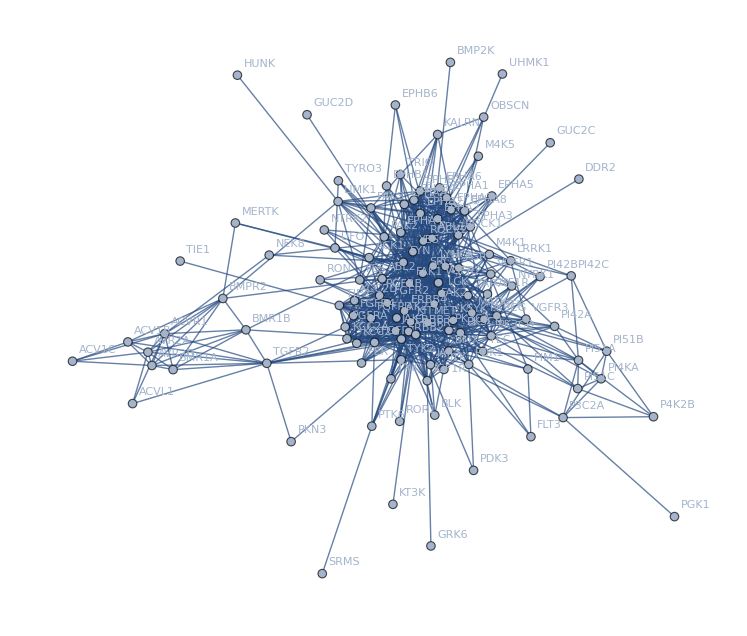

```mathematica
Subgraph[f,Ggreedy["Communities"][[2]],VertexLabels-> flabelstable]
```

```mathematica
fgreedy = CommunityGraphPlot[f,Ggreedy["Communities"],Method->"Hierarchical",VertexLabels -> flabelstable,EdgeStyle->Join[edgeisdrugStyles,edgeisnotdrugStyles]]
```

-Graphics-

```mathematica
fwalktrap = CommunityGraphPlot[f,Gwalktrap["Communities"],Method->"Hierarchical",VertexLabels -> flabelstable,EdgeStyle->Join[edgeisdrugStyles,edgeisnotdrugStyles]];
```

```mathematica
fspectral = CommunityGraphPlot[f,Gspectral,Method->"Hierarchical",VertexLabels -> flabelstable,EdgeStyle->Join[edgeisdrugStyles,edgeisnotdrugStyles]];
```